## Definitions (launch first)

```mathematica
(*selectionDialog[list_]:=DialogInput[{choice={}},Column[{Row[{"Select the list of sensitivities to be plotted by clicking on them:"}],TogglerBar[Dynamic[choice],list,Appearance->"Vertical"],Button["OK",DialogReturn[choice]]}]]*)
selectionDialog[list_,phrase_]:=DialogInput[{choice={}},Column[{Row[{"Select the experiments for which the number of events will be computed. The meaning is ",phrase}],Pane[TogglerBar[Dynamic[choice],list,Appearance->"Vertical"->{Automatic,5}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["OK",DialogReturn[choice]]}]]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
deletecellsopt=dropdownDialog[{"Yes","No"},Row[{"Would you like to remove all the generated output cells?"}]];
If[deletecellsopt=="Yes",FrontEndTokenExecute["DeleteGeneratedCells"]]
```

## HNLs

## List of available sensitivities

```mathematica
filenamesSensitivityTemp=FileNames["*.xls",FileNameJoin[{NotebookDirectory[],"Sensitivity domains/HNLs"}],2];
filenamesSensitivity=Table[Last@FileNameSplit@filenamesSensitivityTemp[[i]],{i,1,Length[filenamesSensitivityTemp],1}];
ParametersSensitivityTemp[i_]:=StringCases[filenamesSensitivity[[i]],"Sensitivity_HNL_MixingPattern_"~~ue__~~"-"~~um__~~"-"~~ut__~~"_type_"~~type__~~"_at_"~~experiment__~~"_Nev="~~Nev__~~"_Npot="~~Npot__~~".xls":>{ue//ToExpression,um//ToExpression,ut//ToExpression,type,experiment,Nev,Npot}][[1]]
ParametersSensitivity=Table[ParametersSensitivityTemp[i],{i,1,Length[filenamesSensitivity],1}];
Print["List of available sensitivities:"]
rowexpl={{"((U^2)_e)/U^2","((U^2)_μ)/U^2","((U^2)_τ)/U^2","Nature","Experiment","N_PoT","N_(ev, min)"}};
Join[rowexpl,ParametersSensitivity]//TableForm
(*Importing constraints*)
BC6excluded=Import[FileNameJoin[{NotebookDirectory[],"contours/BC6-8/current-experiments_e.dat"}],"Table"];
BC7excluded=Import[FileNameJoin[{NotebookDirectory[],"contours/BC6-8/current-experiments_mu.dat"}],"Table"];
BC8excluded=Import[FileNameJoin[{NotebookDirectory[],"contours/BC6-8/current-experiments_tau.dat"}],"Table"];
Print["Selected sensitivities:"]
listSensitivities=selectionDialog[ParametersSensitivity,"{x_e, x_μ, x_τ, Nature, Experiment, N_(ev, min), N_PoT}"];
Join[rowexpl,listSensitivities]//TableForm
SensitivitiesForPlot=Table[Import[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","HNLs",listSensitivities[[i]][[5]],ToString@StringForm["Sensitivity_HNL_MixingPattern_``-``-``_type_``_at_``_Nev=``_Npot=``.xls",Sequence@@listSensitivities[[i]]]}]],{i,1,Length[listSensitivities],1}];
(*If the selected pattern coincides with pure e, mu, or tau mixings, the plot will also include the excluded region*)
pattern=listSensitivities[[All,{1,2,3}]][[1]];
nature=listSensitivities[[All,4]][[1]];
ExcludedRegion=If[nature=="Majorana",If[pattern=={1,0,0},BC6excluded,If[pattern=={0,1,0},BC7excluded,If[pattern=={0,0,1},BC8excluded,{{1,1}}]]],{{1,1}}];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots/HNLs"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots/HNLs"}]]]
```

## Plot

```mathematica
{mminmaxoverall,couplingminmaxoverall}=MinMax[Join[##,1]&@@Table[MinMax[Flatten[SensitivitiesForPlot[[i]],1][[All,#]]],{i,1,Length[SensitivitiesForPlot]}]]&/@{1,2};
LegendsForPlot=Table[Row[{listSensitivities[[i]][[5]],", N_ev ≥ ", listSensitivities[[i]][[6]]}],{i,1,Length[listSensitivities],1}];
ColorsForPlot={{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick, Black},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Black,Dashing[0.02]}};
plotstylelist=Flatten[Table[ConstantArray[ColorsForPlot[[i]],If[MatrixQ[SensitivitiesForPlot[[i]]],1,Length@SensitivitiesForPlot[[i]]]],{i,1,Length[SensitivitiesForPlot],1}],1];
PlotSensitivityHNL=Show[ListLogLogPlot[ExcludedRegion,Joined->True,PlotStyle->{Thick,Gray},Frame-> True,FrameLabel->{"m_N [GeV]" , "U^2"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{1.01mminmaxoverall[[1]],1.1mminmaxoverall[[2]]},{0.05*couplingminmaxoverall[[1]],0.97couplingminmaxoverall[[2]]}},PlotLabel->Style[Row[{"HNLs. ", nature, " nature, pattern =", pattern}],16,Black],Filling->{1->{True,Directive[Gray,Opacity[0.3]]}}],ListLogLogPlot[Cases[SensitivitiesForPlot,_?MatrixQ,All],Joined->True,PlotStyle->plotstylelist],Plot[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{x,0,1},PlotStyle->DeleteDuplicates[plotstylelist],PlotLegends->Placed[Style[#,15]&/@LegendsForPlot,(*{0.24,0.14}*)Right]],Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.5,0.9}]]}]]
Export[FileNameJoin[{NotebookDirectory[],"plots/HNLs/SensitivityHNL.pdf"}],PlotSensitivityHNL]
```

## Scalars

## List of available sensitivities

```mathematica
filenamesSensitivityTemp=FileNames["*.xls",FileNameJoin[{NotebookDirectory[],"Sensitivity domains/Scalars"}],2];
filenamesSensitivity=Table[Last@FileNameSplit@filenamesSensitivityTemp[[i]],{i,1,Length[filenamesSensitivityTemp],1}];
ParametersSensitivityTemp[i_]:=StringCases[filenamesSensitivity[[i]],"Sensitivity_Scalar_at_"~~experiment__~~"_BrhToSS="~~BrhToSS__~~"_Nev="~~Nev__~~"_Npot="~~Npot__~~".xls":>{experiment,BrhToSS//ToExpression,Nev//ToExpression,Npot}][[1]]
ParametersSensitivity=Table[ParametersSensitivityTemp[i],{i,1,Length[filenamesSensitivity],1}];
Print["List of available sensitivities:"]
rowexpl={{"Experiment","Br(h->SS)","N_(ev, min)","N_PoT"}};
Join[rowexpl,ParametersSensitivity]//TableForm
Print["Selected sensitivities:"]
listSensitivities=selectionDialog[ParametersSensitivity,"{Experiment, Br_(h -> SS), N_(ev, min), N_PoT}"];
Join[rowexpl,listSensitivities]//TableForm
SensitivitiesForPlot=Table[Import[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","Scalars",listSensitivities[[i]][[1]],ToString@StringForm["Sensitivity_Scalar_at_``_BrhToSS=``_Nev=``_Npot=``.xls",Sequence@@listSensitivities[[i]]]}]],{i,1,Length[listSensitivities],1}];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots/Scalars"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots/Scalars"}]]]
(*Importing constraints*)
BC4excluded=Import[FileNameJoin[{NotebookDirectory[],"contours/Scalar/scalar-all-experiments.txt"}],"Table"];
```

List of available sensitivities:

Experiment | Br(h->SS) | N_(ev, min) | N_PoT
ANUBIS-ceiling-new | 0. | 2.3 | 2.16e17
ANUBIS-ceiling | 0.01 | 2.3 | 2.16e17
ANUBIS-ceiling | 0. | 2.3 | 2.16e17
ANUBIS-shaft | 0.01 | 2.3 | 2.16e17
ANUBIS-shaft | 0. | 2.3 | 2.16e17
Codex-b | 0. | 2.3 | 2.16e16
DarkQuest-phase-2 | 0. | 2.3 | 1.e20
FACET | 0. | 2.3 | 2.16e17
FASER2 | 0. | 2.3 | 2.16e17
HIKE-dump | 0.01 | 2.3 | 5.e19
HIKE-dump | 0. | 2.3 | 5.e19
LHCb-muon-chamber | 0. | 2.3 | 3.6e15
MATHUSLA | 0.01 | 2.3 | 2.16e17
MATHUSLA | 0. | 2.3 | 2.16e17
SHADOWS-latest | 0. | 2.3 | 5.e19
SHADOWS-LoI | 0. | 2.3 | 5.e19
SHADOWS-LoI-up-to-magnet | 0.01 | 2.3 | 5.e19
SHADOWS-LoI-up-to-magnet | 0. | 2.3 | 5.e19
SHiP-ECN3-Felix | 0.01 | 2.3 | 6.e20
SHiP-ECN3-Felix | 0. | 2.3 | 6.e20
SHiP-ECN3-LoI | 0. | 2.3 | 2.e20
SHiP-ECN3-LoI | 0. | 2.3 | 6.e20
SHiP-ECN3-no-cuts | 0. | 2.3 | 6.e20
SHiP-ECN3 | 0.01 | 2.3 | 2.e20
SHiP-ECN3 | 0.01 | 2.3 | 6.e20
SHiP-ECN3 | 0. | 2.3 | 2.e20
SHiP-ECN3 | 0. | 2.3 | 6.e20

Selected sensitivities:

Experiment | Br(h->SS) | N_(ev, min) | N_PoT
ANUBIS-ceiling-new | 0. | 2.3 | 2.16e17
ANUBIS-ceiling | 0. | 2.3 | 2.16e17

## Plot

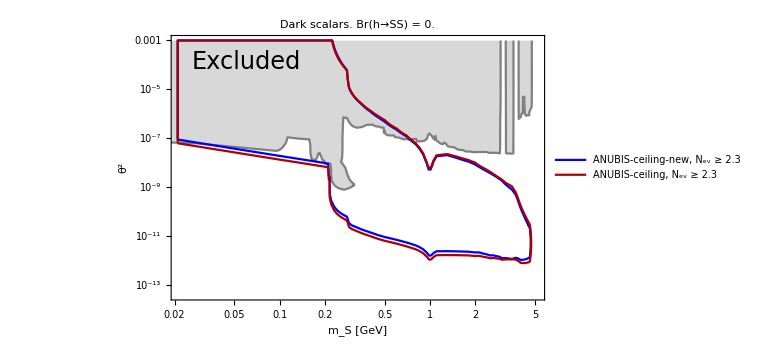

```mathematica
{mminmaxoverall,couplingminmaxoverall}=MinMax[Join[##,1]&@@Table[MinMax[Flatten[SensitivitiesForPlot[[i]],1][[All,#]]],{i,1,Length[SensitivitiesForPlot]}]]&/@{1,2};
LegendsForPlot=Table[Row[{listSensitivities[[i]][[1]],", N_ev ≥ ", listSensitivities[[i]][[3]]}],{i,1,Length[listSensitivities],1}];
ColorsForPlot={{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick, Black},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Black,Dashing[0.02]}};
plotstylelist=Flatten[Table[ConstantArray[ColorsForPlot[[i]],If[MatrixQ[SensitivitiesForPlot[[i]]],1,Length@SensitivitiesForPlot[[i]]]],{i,1,Length[SensitivitiesForPlot],1}],1];
PlotSensitivityScalar=Show[ListLogLogPlot[BC4excluded,Joined->True,PlotStyle->{Thick,Gray},Frame-> True,FrameLabel->{"m_S [GeV]" , "θ^2"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{1.01mminmaxoverall[[1]],1.1mminmaxoverall[[2]]},{0.05*couplingminmaxoverall[[1]],0.99couplingminmaxoverall[[2]]}},PlotLabel->Style[Row[{"Dark scalars. Br(h→SS) = ",listSensitivities[[1]][[2]]}],18,Black],Filling->{1->{True,Directive[Gray,Opacity[0.3]]}}],ListLogLogPlot[Cases[SensitivitiesForPlot,_?MatrixQ,All],Joined->True,PlotStyle->plotstylelist],Plot[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{x,0,1},PlotStyle->DeleteDuplicates[plotstylelist],PlotLegends->Placed[Style[#,15]&/@LegendsForPlot,(*{0.24,0.14}*)Right]],Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.2,0.9}]]}]]
Export[FileNameJoin[{NotebookDirectory[],"plots/Scalars/SensitivityScalar.pdf"}],PlotSensitivityScalar]
```

```mathematica
6.07*√2
```

8.58428

## Dark photons

## List of available sensitivities

```mathematica
filenamesSensitivityTemp=FileNames["*.xls",FileNameJoin[{NotebookDirectory[],"Sensitivity domains/Dark photons"}],2];
filenamesSensitivity=Table[Last@FileNameSplit@filenamesSensitivityTemp[[i]],{i,1,Length[filenamesSensitivityTemp],1}];
ParametersSensitivityTemp[i_]:=StringCases[filenamesSensitivity[[i]],"Sensitivity_DP_at_"~~experiment__~~"_Nev="~~Nev__~~"_Npot="~~Npot__~~".xls":>{experiment,Nev//ToExpression,Npot}][[1]]
ParametersSensitivity=Table[ParametersSensitivityTemp[i],{i,1,Length[filenamesSensitivity],1}];
Print["List of available sensitivities:"]
rowexpl={{"Experiment","N_(ev, min)","N_PoT"}};
Join[rowexpl,ParametersSensitivity]//TableForm
Print["Selected sensitivities:"]
listSensitivities=selectionDialog[ParametersSensitivity,"{Experiment, N_(ev, min), N_PoT}"];
Join[rowexpl,listSensitivities]//TableForm
SensitivitiesForPlot=Table[Import[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","Dark photons",listSensitivities[[i]][[1]],ToString@StringForm["Sensitivity_DP_at_``_Nev=``_Npot=``.xls",Sequence@@listSensitivities[[i]]]}]],{i,1,Length[listSensitivities],1}];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots/Dark photons"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots/Dark photons"}]]]
(*Importing constraints*)
{BC1excluded1,BC1excluded2,BC1excluded3,BC1excludedCosmo}=Import[FileNameJoin[{NotebookDirectory[],"contours/BC1/",#}],"Table"]&/@{"BC1-excluded-1.txt","BC1-excluded-2.txt","BC1-excluded-3.txt","BC1-excluded-cosmo.txt"};
```

## Plot

```mathematica
{mminmaxoverall,couplingminmaxoverall}=MinMax[Join[##,1]&@@Table[MinMax[Flatten[SensitivitiesForPlot[[i]],1][[All,#]]],{i,1,Length[SensitivitiesForPlot]}]]&/@{1,2};
LegendsForPlot=Table[Row[{listSensitivities[[i]][[1]],", N_ev ≥ ",listSensitivities[[i]][[2]]}],{i,1,Length[listSensitivities],1}];
ColorsForPlot={{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick, Black},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Black,Dashing[0.02]}};
plotstylelist=Flatten[Table[ConstantArray[ColorsForPlot[[i]],If[MatrixQ[SensitivitiesForPlot[[i]]],1,Length@SensitivitiesForPlot[[i]]]],{i,1,Length[SensitivitiesForPlot],1}],1];
PlotSensitivityDP=Show[ListLogLogPlot[{BC1excluded1,BC1excluded2,BC1excluded3,BC1excludedCosmo},Joined->True,PlotStyle->{{Thick,Gray},{Thick,Gray},{Thick,Gray},{Thick,Gray},{Thick,Gray}},Frame-> True,FrameLabel->{"m_V [GeV]" , "ϵ^2"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{1.01mminmaxoverall[[1]],1.1mminmaxoverall[[2]]},{0.05*couplingminmaxoverall[[1]],100couplingminmaxoverall[[2]]}},PlotLabel->Style[Row[{"Dark photons"}],18,Black],Filling->{1->{True,Directive[Gray,Opacity[0.3]]},2->{True,Directive[Gray,Opacity[0.3]]},3->{True,Directive[Gray,Opacity[0.3]]},4->{True,Directive[Gray,Opacity[0.1]]}}],ListLogLogPlot[Cases[SensitivitiesForPlot,_?MatrixQ,All],Joined->True,PlotStyle->plotstylelist],Plot[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{x,0,1},PlotStyle->DeleteDuplicates[plotstylelist],PlotLegends->Placed[Style[#,15]&/@LegendsForPlot,(*{0.24,0.14}*)Right]],Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.14,0.5}]]}]]
Export[FileNameJoin[{NotebookDirectory[],"plots/Dark photons/SensitivityDP.pdf"}],PlotSensitivityDP]
```

## ALPs coupled to photons

## List of available sensitivities

```mathematica
filenamesSensitivityTemp=FileNames["*.xls",FileNameJoin[{NotebookDirectory[],"Sensitivity domains/ALPs with photon coupling"}],2];
filenamesSensitivity=Table[Last@FileNameSplit@filenamesSensitivityTemp[[i]],{i,1,Length[filenamesSensitivityTemp],1}];
ParametersSensitivityTemp[i_]:=StringCases[filenamesSensitivity[[i]],"Sensitivity_ALP-photon_at_"~~experiment__~~"_Nev="~~Nev__~~"_Npot="~~Npot__~~".xls":>{experiment,Nev//ToExpression,Npot}][[1]]
ParametersSensitivity=Table[ParametersSensitivityTemp[i],{i,1,Length[filenamesSensitivity],1}];
Print["List of available sensitivities:"]
rowexpl={{"Experiment","N_(ev, min)","N_PoT"}};
Join[rowexpl,ParametersSensitivity]//TableForm
listSensitivities=selectionDialog[ParametersSensitivity,"{Experiment, N_(ev, min), N_PoT}"];
Print["Selected sensitivities:"]
Join[rowexpl,listSensitivities]//TableForm
SensitivitiesForPlot=Table[Import[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with photon coupling",listSensitivities[[i]][[1]],ToString@StringForm["Sensitivity_ALP-photon_at_``_Nev=``_Npot=``.xls",Sequence@@listSensitivities[[i]]]}]],{i,1,Length[listSensitivities],1}];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots/ALPs with photon coupling"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots/ALPs with photon coupling"}]]]
(*Importing constraints*)
BC9excluded=Import[FileNameJoin[{NotebookDirectory[],"contours/BC9/BC9-excluded.txt"}],"Table"];
```

## Plot

```mathematica
{mminmaxoverall,couplingminmaxoverall}=MinMax[Join[##,1]&@@Table[MinMax[Flatten[SensitivitiesForPlot[[i]],1][[All,#]]],{i,1,Length[SensitivitiesForPlot]}]]&/@{1,2};
LegendsForPlot=Table[Row[{listSensitivities[[i]][[1]],", N_ev ≥ ", listSensitivities[[i]][[2]]}],{i,1,Length[listSensitivities],1}];
ColorsForPlot={{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick, Black},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Black,Dashing[0.02]}};
plotstylelist=Flatten[Table[ConstantArray[ColorsForPlot[[i]],If[MatrixQ[SensitivitiesForPlot[[i]]],1,Length@SensitivitiesForPlot[[i]]]],{i,1,Length[SensitivitiesForPlot],1}],1];
PlotSensitivityALPphoton=Show[ListLogLogPlot[BC9excluded,Joined->True,PlotStyle->{Thick,Gray},Frame-> True,FrameLabel->{"m_a [GeV]" , "g_a [GeV^-1]"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{1.01mminmaxoverall[[1]],1.1mminmaxoverall[[2]]},{0.05*couplingminmaxoverall[[1]],0.99couplingminmaxoverall[[2]]}},PlotLabel->Style[Row[{"ALPs coupled to photons"}],18,Black],Filling->{1->{True,Directive[Gray,Opacity[0.3]]}}],ListLogLogPlot[Cases[SensitivitiesForPlot,_?MatrixQ,All],Joined->True,PlotStyle->plotstylelist],Plot[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{x,0,1},PlotStyle->DeleteDuplicates[plotstylelist],PlotLegends->Placed[Style[#,15]&/@LegendsForPlot,(*{0.24,0.14}*)Right]],Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.2,0.5}]]}]]
Export[FileNameJoin[{NotebookDirectory[],"plots/ALPs with photon coupling/SensitivityALPphoton.pdf"}],PlotSensitivityALPphoton]
```

## ALPs coupled to fermions

## List of available sensitivities

```mathematica
filenamesSensitivityTemp=FileNames["*.xls",FileNameJoin[{NotebookDirectory[],"Sensitivity domains/ALPs with fermion coupling"}],2];
filenamesSensitivity=Table[Last@FileNameSplit@filenamesSensitivityTemp[[i]],{i,1,Length[filenamesSensitivityTemp],1}];
ParametersSensitivityTemp[i_]:=StringCases[filenamesSensitivity[[i]],"Sensitivity_ALP-fermion_at_"~~experiment__~~"_Nev="~~Nev__~~"_Npot="~~Npot__~~".xls":>{experiment,Nev//ToExpression,Npot}][[1]]
ParametersSensitivity=Table[ParametersSensitivityTemp[i],{i,1,Length[filenamesSensitivity],1}];
Print["List of available sensitivities:"]
rowexpl={{"Experiment","N_(ev, min)","N_Pot"}};
Join[rowexpl,ParametersSensitivity]//TableForm
listSensitivities=selectionDialog[ParametersSensitivity,"{Experiment, N_(ev, min), N_PoT}"];
Print["Selected sensitivities:"]
Join[rowexpl,listSensitivities]//TableForm
SensitivitiesForPlot=Table[Import[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with fermion coupling",listSensitivities[[i]][[1]],ToString@StringForm["Sensitivity_ALP-fermion_at_``_Nev=``_Npot=``.xls",Sequence@@listSensitivities[[i]]]}]],{i,1,Length[listSensitivities],1}];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots/ALPs with fermion coupling"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots/ALPs with fermion coupling"}]]]
(*Importing constraints*)
BC10excluded=Import[FileNameJoin[{NotebookDirectory[],"contours/BC10/BC10-excluded.txt"}],"Table"];
```

## Plot

```mathematica
{mminmaxoverall,couplingminmaxoverall}=MinMax[Join[##,1]&@@Table[MinMax[Flatten[SensitivitiesForPlot[[i]],1][[All,#]]],{i,1,Length[SensitivitiesForPlot]}]]&/@{1,2};
LegendsForPlot=Table[Row[{listSensitivities[[i]][[1]],", N_ev ≥ ",listSensitivities[[i]][[2]]}],{i,1,Length[listSensitivities],1}];
ColorsForPlot={{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick, Black},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Black,Dashing[0.02]}};
plotstylelist=Flatten[Table[ConstantArray[ColorsForPlot[[i]],If[MatrixQ[SensitivitiesForPlot[[i]]],1,Length@SensitivitiesForPlot[[i]]]],{i,1,Length[SensitivitiesForPlot],1}],1];
PlotSensitivityALPfermion=Show[ListLogLogPlot[BC10excluded,Joined->True,PlotStyle->{Thick,Gray},Frame-> True,FrameLabel->{"m_a [GeV]" , "g_Y"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{1.01mminmaxoverall[[1]],1.1mminmaxoverall[[2]]},{0.05*couplingminmaxoverall[[1]],0.99couplingminmaxoverall[[2]]}},PlotLabel->Style[Row[{"ALPs coupled to fermions"}],18,Black],Filling->{1->{True,Directive[Gray,Opacity[0.3]]}}],ListLogLogPlot[Cases[SensitivitiesForPlot,_?MatrixQ,All],Joined->True,PlotStyle->plotstylelist],Plot[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{x,0,1},PlotStyle->DeleteDuplicates[plotstylelist],PlotLegends->Placed[Style[#,15]&/@LegendsForPlot,(*{0.24,0.14}*)Right]],Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.6,0.94}]]}]]
Export[FileNameJoin[{NotebookDirectory[],"plots/ALPs with fermion coupling/SensitivityALPfermion.pdf"}],PlotSensitivityALPfermion]
```

## ALPs coupled to gluons

## List of available sensitivities

```mathematica
filenamesSensitivityTemp=FileNames["*.xls",FileNameJoin[{NotebookDirectory[],"Sensitivity domains/ALPs with gluon coupling"}],2];
filenamesSensitivity=Table[Last@FileNameSplit@filenamesSensitivityTemp[[i]],{i,1,Length[filenamesSensitivityTemp],1}];
ParametersSensitivityTemp[i_]:=StringCases[filenamesSensitivity[[i]],"Sensitivity_ALP-gluon_at_"~~experiment__~~"_Nev="~~Nev__~~"_Npot="~~Npot__~~".xls":>{experiment,Nev//ToExpression,Npot}][[1]]
ParametersSensitivity=Table[ParametersSensitivityTemp[i],{i,1,Length[filenamesSensitivity],1}];
Print["List of available sensitivities:"]
rowexpl={{"Experiment","N_(ev, min)","N_PoT"}};
Join[rowexpl,ParametersSensitivity]//TableForm
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots/ALPs with gluon coupling"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots/ALPs with gluon coupling"}]]]
listSensitivities=selectionDialog[ParametersSensitivity,"{Experiment, N_(ev, min), N_PoT}"];
Print["Selected sensitivities:"]
Join[rowexpl,listSensitivities]//TableForm
SensitivitiesForPlot=Table[Import[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with gluon coupling",listSensitivities[[i]][[1]],ToString@StringForm["Sensitivity_ALP-gluon_at_``_Nev=``_Npot=``.xls",Sequence@@listSensitivities[[i]]]}]],{i,1,Length[listSensitivities],1}];
(*Importing constraints*)
BC11excluded1=Import[FileNameJoin[{NotebookDirectory[],"contours/BC11/BC11-CHARM.txt"}],"Table"];
BC11excluded2=Import[FileNameJoin[{NotebookDirectory[],"contours/BC11/BC11-no-CHARM.txt"}],"Table"];
```

## Plot

```mathematica
{mminmaxoverall,couplingminmaxoverall}=MinMax[Join[##,1]&@@Table[MinMax[Flatten[SensitivitiesForPlot[[i]],1][[All,#]]],{i,1,Length[SensitivitiesForPlot]}]]&/@{1,2};
LegendsForPlot=Table[Row[{listSensitivities[[i]][[1]],", N_ev ≥ ", listSensitivities[[i]][[2]]}],{i,1,Length[listSensitivities],1}];
ColorsForPlot={{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick, Black},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Black,Dashing[0.02]}};
plotstylelist=Flatten[Table[ConstantArray[ColorsForPlot[[i]],If[MatrixQ[SensitivitiesForPlot[[i]]],1,Length@SensitivitiesForPlot[[i]]]],{i,1,Length[SensitivitiesForPlot],1}],1];
PlotSensitivityALPgluon=Show[ListLogLogPlot[{BC11excluded1,BC11excluded2},Joined->True,PlotStyle->{{Thick,Gray},{Thick,Gray},{Thick,Gray}},Frame-> True,FrameLabel->{"m_a [GeV]" , "f_G [GeV^-1]"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{Max[1.01mminmaxoverall[[1]],0.2],1.1mminmaxoverall[[2]]},{0.05*couplingminmaxoverall[[1]],0.99couplingminmaxoverall[[2]]}},PlotLabel->Style[Row[{"ALPs coupled to gluons"}],18,Black],Filling->{1->{True,Directive[Gray,Opacity[0.3]]},2->{True,Directive[Gray,Opacity[0.3]]}}],ListLogLogPlot[Cases[SensitivitiesForPlot,_?MatrixQ,All],Joined->True,PlotStyle->plotstylelist],Plot[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{x,0,1},PlotStyle->DeleteDuplicates[plotstylelist],PlotLegends->Placed[Style[#,15]&/@LegendsForPlot,(*{0.24,0.14}*)Right]],Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.15,0.7}]]}]]
Export[FileNameJoin[{NotebookDirectory[],"plots/ALPs with gluon coupling/SensitivityALPgluon.pdf"}],PlotSensitivityALPgluon]
```

## B-L

## List of available sensitivities

```mathematica
filenamesSensitivityTemp=FileNames["*.xls",FileNameJoin[{NotebookDirectory[],"Sensitivity domains/B-L"}],2];
filenamesSensitivity=Table[Last@FileNameSplit@filenamesSensitivityTemp[[i]],{i,1,Length[filenamesSensitivityTemp],1}];
ParametersSensitivityTemp[i_]:=StringCases[filenamesSensitivity[[i]],"Sensitivity_B-L_at_"~~experiment__~~"_Nev="~~Nev__~~"_Npot="~~Npot__~~".xls":>{experiment,Nev//ToExpression,Npot}][[1]]
ParametersSensitivity=Table[ParametersSensitivityTemp[i],{i,1,Length[filenamesSensitivity],1}];
Print["List of available sensitivities:"]
rowexpl={{"Experiment","N_(ev, min)","N_PoT"}};
Join[rowexpl,ParametersSensitivity]//TableForm
listSensitivities=selectionDialog[ParametersSensitivity,"{Experiment, N_(ev, min), N_PoT}"];
Print["Selected sensitivities:"]
Join[rowexpl,listSensitivities]//TableForm
SensitivitiesForPlot=Table[Import[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","B-L",listSensitivities[[i]][[1]],ToString@StringForm["Sensitivity_B-L_at_``_Nev=``_Npot=``.xls",Sequence@@listSensitivities[[i]]]}]],{i,1,Length[listSensitivities],1}];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots/B-L"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots/B-L"}]]]
(*Importing constraints*)
BLexcluded=Import[FileNameJoin[{NotebookDirectory[],"contours/B-L/B-L-excluded.txt"}],"Table"];
```

## Plot

```mathematica
{mminmaxoverall,couplingminmaxoverall}=MinMax[Join[##,1]&@@Table[MinMax[Flatten[SensitivitiesForPlot[[i]],1][[All,#]]],{i,1,Length[SensitivitiesForPlot]}]]&/@{1,2};
LegendsForPlot=Table[Row[{listSensitivities[[i]][[1]],", N_ev ≥ ",listSensitivities[[i]][[2]]}],{i,1,Length[listSensitivities],1}];
ColorsForPlot={{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick, Black},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Black,Dashing[0.02]}};
plotstylelist=Flatten[Table[ConstantArray[ColorsForPlot[[i]],If[MatrixQ[SensitivitiesForPlot[[i]]],1,Length@SensitivitiesForPlot[[i]]]],{i,1,Length[SensitivitiesForPlot],1}],1];
PlotSensitivityBL=Show[ListLogLogPlot[BLexcluded,Joined->True,PlotStyle->{Thick,Gray},Frame-> True,FrameLabel->{"m_V [GeV]" , "α_B"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{1.01mminmaxoverall[[1]],1.1mminmaxoverall[[2]]},{0.05*couplingminmaxoverall[[1]],0.99couplingminmaxoverall[[2]]}},PlotLabel->Style[Row[{"U_(B - L)(1) mediator"}],18,Black],Filling->{1->{True,Directive[Gray,Opacity[0.3]]}}],ListLogLogPlot[Cases[SensitivitiesForPlot,_?MatrixQ,All],Joined->True,PlotStyle->plotstylelist],Plot[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{x,0,1},PlotStyle->DeleteDuplicates[plotstylelist],PlotLegends->Placed[Style[#,15]&/@LegendsForPlot,(*{0.24,0.14}*)Right]],Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.2,0.5}]],Text[Style["e)",30,Black],Scaled[{0.05,0.9}]]}]]
Export[FileNameJoin[{NotebookDirectory[],"plots/B-L/SensitivityB-L.pdf"}],PlotSensitivityBL]
```

## B-3 L_μ

## List of available sensitivities

```mathematica
filenamesSensitivityTemp=FileNames["*.xls",FileNameJoin[{NotebookDirectory[],"Sensitivity domains/B-3Lmu"}],2];
filenamesSensitivity=Table[Last@FileNameSplit@filenamesSensitivityTemp[[i]],{i,1,Length[filenamesSensitivityTemp],1}];
ParametersSensitivityTemp[i_]:=StringCases[filenamesSensitivity[[i]],"Sensitivity_B-3Lmu_at_"~~experiment__~~"_Nev="~~Nev__~~"_Npot="~~Npot__~~".xls":>{experiment,Nev//ToExpression,Npot}][[1]]
ParametersSensitivity=Table[ParametersSensitivityTemp[i],{i,1,Length[filenamesSensitivity],1}];
Print["List of available sensitivities:"]
rowexpl={{"Experiment","N_(ev, min)","N_PoT"}};
Join[rowexpl,ParametersSensitivity]//TableForm
listSensitivities=selectionDialog[ParametersSensitivity,"{Experiment, N_(ev, min), N_PoT}"];
Print["Selected sensitivities:"]
Join[rowexpl,listSensitivities]//TableForm
SensitivitiesForPlot=Table[Import[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","B-3Lmu",listSensitivities[[i]][[1]],ToString@StringForm["Sensitivity_B-3Lmu_at_``_Nev=``_Npot=``.xls",Sequence@@listSensitivities[[i]]]}]],{i,1,Length[listSensitivities],1}];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots/B-3Lmu"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots/B-3Lmu"}]]]
(*Importing constraints*)
BLexcluded=Import[FileNameJoin[{NotebookDirectory[],"contours/B-L/B-L-excluded.txt"}],"Table"];
```

## Plot

```mathematica
{mminmaxoverall,couplingminmaxoverall}=MinMax[Join[##,1]&@@Table[MinMax[Flatten[SensitivitiesForPlot[[i]],1][[All,#]]],{i,1,Length[SensitivitiesForPlot]}]]&/@{1,2};
LegendsForPlot=Table[Row[{listSensitivities[[i]][[1]],", N_ev ≥ ",listSensitivities[[i]][[2]]}],{i,1,Length[listSensitivities],1}];
ColorsForPlot={{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick, Black},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Black,Dashing[0.02]}};
plotstylelist=Flatten[Table[ConstantArray[ColorsForPlot[[i]],If[MatrixQ[SensitivitiesForPlot[[i]]],1,Length@SensitivitiesForPlot[[i]]]],{i,1,Length[SensitivitiesForPlot],1}],1];
PlotSensitivityBL=Show[ListLogLogPlot[BLexcluded,Joined->True,PlotStyle->{Thick,Gray},Frame-> True,FrameLabel->{"m_V [GeV]" , "α_B"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{1.01mminmaxoverall[[1]],1.1mminmaxoverall[[2]]},{0.05*couplingminmaxoverall[[1]],0.99couplingminmaxoverall[[2]]}},PlotLabel->Style[Row[{"U_(B - 3 SubscriptBox[L, μ])(1) mediator"}],18,Black],Filling->{1->{True,Directive[Gray,Opacity[0.3]]}}],ListLogLogPlot[Cases[SensitivitiesForPlot,_?MatrixQ,All],Joined->True,PlotStyle->plotstylelist],Plot[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{x,0,1},PlotStyle->DeleteDuplicates[plotstylelist],PlotLegends->Placed[Style[#,15]&/@LegendsForPlot,(*{0.24,0.14}*)Right]],Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.2,0.5}]]}]]
Export[FileNameJoin[{NotebookDirectory[],"plots/B-3Lmu/SensitivityB-3Lmu.pdf"}],PlotSensitivityBL]
```

## B-3 L_e-L_μ+L_τ

## List of available sensitivities

```mathematica
filenamesSensitivityTemp=FileNames["*.xls",FileNameJoin[{NotebookDirectory[],"Sensitivity domains/B-3Le-Lmu+Ltau"}],2];
filenamesSensitivity=Table[Last@FileNameSplit@filenamesSensitivityTemp[[i]],{i,1,Length[filenamesSensitivityTemp],1}];
ParametersSensitivityTemp[i_]:=StringCases[filenamesSensitivity[[i]],"Sensitivity_B-3Le-Lmu+Ltau_at_"~~experiment__~~"_Nev="~~Nev__~~"_Npot="~~Npot__~~".xls":>{experiment,Nev//ToExpression,Npot}][[1]]
ParametersSensitivity=Table[ParametersSensitivityTemp[i],{i,1,Length[filenamesSensitivity],1}];
Print["List of available sensitivities:"]
rowexpl={{"Experiment","N_(ev, min)","N_PoT"}};
Join[rowexpl,ParametersSensitivity]//TableForm
listSensitivities=selectionDialog[ParametersSensitivity,"{Experiment, N_(ev, min), N_PoT}"];
Print["Selected sensitivities:"]
Join[rowexpl,listSensitivities]//TableForm
SensitivitiesForPlot=Table[Import[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","B-3Le-Lmu+Ltau",listSensitivities[[i]][[1]],ToString@StringForm["Sensitivity_B-3Le-Lmu+Ltau_at_``_Nev=``_Npot=``.xls",Sequence@@listSensitivities[[i]]]}]],{i,1,Length[listSensitivities],1}];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots/B-3Le-Lmu+Ltau"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots/B-3Le-Lmu+Ltau"}]]]
(*Importing constraints*)
BLexcluded=Import[FileNameJoin[{NotebookDirectory[],"contours/B-L/B-L-excluded.txt"}],"Table"];
```

## Plot

```mathematica
{mminmaxoverall,couplingminmaxoverall}=MinMax[Join[##,1]&@@Table[MinMax[Flatten[SensitivitiesForPlot[[i]],1][[All,#]]],{i,1,Length[SensitivitiesForPlot]}]]&/@{1,2};
LegendsForPlot=Table[Row[{listSensitivities[[i]][[1]],", N_ev ≥ ",listSensitivities[[i]][[2]]}],{i,1,Length[listSensitivities],1}];
ColorsForPlot={{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick, Black},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Black,Dashing[0.02]}};
plotstylelist=Flatten[Table[ConstantArray[ColorsForPlot[[i]],If[MatrixQ[SensitivitiesForPlot[[i]]],1,Length@SensitivitiesForPlot[[i]]]],{i,1,Length[SensitivitiesForPlot],1}],1];
PlotSensitivityBL=Show[ListLogLogPlot[BLexcluded,Joined->True,PlotStyle->{Thick,Gray},Frame-> True,FrameLabel->{"m_V [GeV]" , "α_B"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{1.01mminmaxoverall[[1]],1.1mminmaxoverall[[2]]},{0.05*couplingminmaxoverall[[1]],0.99couplingminmaxoverall[[2]]}},PlotLabel->Style[Row[{"U_(B - 3 SubscriptBox[L, e] - SubscriptBox[L, μ] + SubscriptBox[L, τ])(1) mediator"}],18,Black],Filling->{1->{True,Directive[Gray,Opacity[0.3]]}}],ListLogLogPlot[Cases[SensitivitiesForPlot,_?MatrixQ,All],Joined->True,PlotStyle->plotstylelist],Plot[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{x,0,1},PlotStyle->DeleteDuplicates[plotstylelist],PlotLegends->Placed[Style[#,15]&/@LegendsForPlot,(*{0.24,0.14}*)Right]],Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.2,0.5}]]}]]
Export[FileNameJoin[{NotebookDirectory[],"plots/B-3Le-Lmu+Ltau/SensitivityB-3Le-Lmu+Ltau.pdf"}],PlotSensitivityBL]
```

## B-L_e-3 L_μ+L_τ

## List of available sensitivities

```mathematica
filenamesSensitivityTemp=FileNames["*.xls",FileNameJoin[{NotebookDirectory[],"Sensitivity domains/B-Le-3Lmu+Ltau"}],2];
filenamesSensitivity=Table[Last@FileNameSplit@filenamesSensitivityTemp[[i]],{i,1,Length[filenamesSensitivityTemp],1}];
ParametersSensitivityTemp[i_]:=StringCases[filenamesSensitivity[[i]],"Sensitivity_B-Le-3Lmu+Ltau_at_"~~experiment__~~"_Nev="~~Nev__~~"_Npot="~~Npot__~~".xls":>{experiment,Nev//ToExpression,Npot}][[1]]
ParametersSensitivity=Table[ParametersSensitivityTemp[i],{i,1,Length[filenamesSensitivity],1}];
Print["List of available sensitivities:"]
rowexpl={{"Experiment","N_(ev, min)","N_PoT"}};
Join[rowexpl,ParametersSensitivity]//TableForm
listSensitivities=selectionDialog[ParametersSensitivity,"{Experiment, N_(ev, min), N_PoT}"];
Print["Selected sensitivities:"]
Join[rowexpl,listSensitivities]//TableForm
SensitivitiesForPlot=Table[Import[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","B-Le-3Lmu+Ltau",listSensitivities[[i]][[1]],ToString@StringForm["Sensitivity_B-Le-3Lmu+Ltau_at_``_Nev=``_Npot=``.xls",Sequence@@listSensitivities[[i]]]}]],{i,1,Length[listSensitivities],1}];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"plots/B-Le-3Lmu+Ltau"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"plots/B-Le-3Lmu+Ltau"}]]]
(*Importing constraints*)
BLexcluded=Import[FileNameJoin[{NotebookDirectory[],"contours/B-L/B-L-excluded.txt"}],"Table"];
```

## Plot

```mathematica
{mminmaxoverall,couplingminmaxoverall}=MinMax[Join[##,1]&@@Table[MinMax[Flatten[SensitivitiesForPlot[[i]],1][[All,#]]],{i,1,Length[SensitivitiesForPlot]}]]&/@{1,2};
LegendsForPlot=Table[Row[{listSensitivities[[i]][[1]],", N_ev ≥ ",listSensitivities[[i]][[2]]}],{i,1,Length[listSensitivities],1}];
ColorsForPlot={{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick, Black},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Cyan,Dashing[0.02]},{Thick,Magenta,Dashing[0.02]},{Thick,Black,Dashing[0.02]}};
plotstylelist=Flatten[Table[ConstantArray[ColorsForPlot[[i]],If[MatrixQ[SensitivitiesForPlot[[i]]],1,Length@SensitivitiesForPlot[[i]]]],{i,1,Length[SensitivitiesForPlot],1}],1];
PlotSensitivityBL=Show[ListLogLogPlot[BLexcluded,Joined->True,PlotStyle->{Thick,Gray},Frame-> True,FrameLabel->{"m_V [GeV]" , "α_B"},FrameStyle->Directive[Black, 23],ImageSize->Large,PlotRange->{{1.01mminmaxoverall[[1]],1.1mminmaxoverall[[2]]},{0.05*couplingminmaxoverall[[1]],0.99couplingminmaxoverall[[2]]}},PlotLabel->Style[Row[{"U_(B - SubscriptBox[L, e] - 3 SubscriptBox[L, μ] + SubscriptBox[L, τ])(1) mediator"}],18,Black],Filling->{1->{True,Directive[Gray,Opacity[0.3]]}}],ListLogLogPlot[Cases[SensitivitiesForPlot,_?MatrixQ,All],Joined->True,PlotStyle->plotstylelist],Plot[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{x,0,1},PlotStyle->DeleteDuplicates[plotstylelist],PlotLegends->Placed[Style[#,15]&/@LegendsForPlot,(*{0.24,0.14}*)Right]],Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.2,0.5}]]}]]
Export[FileNameJoin[{NotebookDirectory[],"plots/B-Le-3Lmu+Ltau/SensitivityB-Le-3Lmu+Ltau.pdf"}],PlotSensitivityBL]
```